# Synthesizing idealized pronunciations of all possible IPA sounds

Chengmin Xu
WSRP 2025

The International Phonetic Alphabet contains over 100 symbols for consonants and vowels to document human language, making the phonetic transcription system extremely useful for linguistics fieldwork; however, the IPA has its limitations, as a wider majority of sounds lack unique classification symbols or simply are too scarce in detail for greater accuracy in transcription. This project exhibits the theoretical pronunciations of IPA sounds that lack official classifications through the process of synthesizing audio using mechanically generated or altered voice based on real human speech data. While synthesized audio realizations of certain vowels and consonants are often devoid of the naturalness of human articulation, it provides an adequate model that approximates the rough pronunciation of such phonetic sounds. Ultimately, this project seeks to broaden IPA access and resources for linguists, provide a practical pronunciation tool for academic and recreational use establish a basic audio‑analysis and computational framework for future phonetics and linguistics research.

## 1 Introduction

The International Phonetic Alphabet (IPA) is a useful system for phonetic transcriptions—it covers the phonetics of virtually all languages in the world, all sounds producible by the human mouth. First published in 1888, the original IPA contained only 30 consonant symbols and 13 vowel symbols; today, the IPA has expanded to accommodate for 59 consonants and 28 vowels, with the latest sound added being the labiodental flap, [ⱱ], as of 2005. It also includes 43 non-pulmonic consonants (e.g. clicks, implosives, and ejectives), 52 diacritics and modifiers, as well as 4 suprasegmental marks to indicate more precise features of languages, such as stress, pitch, and intonation. With linguists around the world using it as the benchmark for their research, it’s needless to say that the IPA acts as the center of phonological documentation in the linguistics world, instrumental to fieldwork and linguistic data analysis.

However, the IPA chart, though efficient and convenient, isn’t perfect. In many cases, even with diacritics and precision markers, documented pronunciations often lose detail compared to their original articulations due to the complexity of sounds produced by the human mouth. As such, linguists struggle with finding exact transcriptions of sounds, instead having to settle for approximations of certain pronunciations. 

Consider the following chart of pulmonic consonants (consonants with pulmonic egressive airstream mechanism, i.e., air flows outwards to produce sound).

-Graphics-

Although the IPA consonant chart contains 59 classified consonants, the other 117 sounds still lack an IPA symbol, 32 of which are grayed-out and deemed impossible. Yet out of these 117 unrepresented consonants, 85 sounds are not grayed-out—an indication that while these consonants are not officially documented or naturally produced phonemically in any known languages, they are still theoretically possible to pronounce.

The same can be said for the IPA vowel chart (the trapezoidal shape representing various locations within the human mouth):

-Graphics-

Evidently, despite there being 28 symbols for vowel transcription, most of the trapezoid is filled with blank space in the middle, meaning that there are plenty of vowels left off the documentation or are documented roughly or inaccurately. This begs the question: is there a way to generate computer-synthesized audio to model the theoretical pronunciation of consonants that lack a symbol and vowels at any point in the vowel space? Indeed, by analyzing audio measurements, spectrograms, and complex frequency data, it is possible to edit audio and mechanically produce sounds based on real human pronunciations. The concept behind this is related and similar to text-to-speech functions in software such as Google Translate and Apple Siri. 

A simple example of text-to-audio synthesis can be seen in the Wolfram integrated environment via the SpeechSynthesize function:

```mathematica
SpeechSynthesize["Hello world!"]
```

The key difference between traditional text-to-speech and IPA-to-audio is a difference between synthesizing words versus synthesizing sounds; while traditional text-to-speech technology generates audio based on words from known databases, the scope of an IPA to audio function would require audio synthesis at the phonetic level, modifying individual sounds. Hence, using Wolfram language, this project seeks to computationally synthesize all IPA sounds, including vowels, pulmonic consonants, non-pulmonic consonants, as well as varying pitch in synthesized speech, to create a digital or “idealized” version of pronunciations for future reference. This project ultimately intends to expand the accessibility of the IPA and provide more IPA resources to linguists and linguistics academia, to help facilitate and improve pronunciation for studiers of foreign language, and to serve as a rudimentary model integrating audio analysis, spectral manipulation, and computation into future linguistics and phonetics research.

## 2 Approach

### 2.1 Data

The project utilized raw data of every consonant and vowel sound compiled and imported from www.ipachart.com, a database of IPA pronunciations by speaker Peter Isotalo, standardized and archived by UCLA Phonetics Lab. For ease of accessibility, each data point was tied to an IPA symbol, sorted into two lists, and made into separate associations, IPAVowels and IPAConsonants:

Ex. Voiceless alveolo-palatal fricative [ɕ]:

```mathematica
IPAConsonants["ɕ"]
```

Ex 2. Close front rounded vowel [y]:

```mathematica
IPAVowels["y"]
```

Recordings from the dataset presented each consonant word-initially and word-medially, e.g., [ɕaː aɕaː], and each monophthong in lengthened form, e.g., [yː]. In total, 119 data points were used, including samples of 28 vowels, 59 pulmonic consonants and 32 non-pulmonic consonants and special symbols. The complete dataset for consonants and vowels can be accessed in Section 6.1 in the Appendix.

### 2.2 Constructing Audio

There are a few approaches to constructing synthesized audio based on human pronunciation data. The simplest concept is by modifying the spectrogram data obtained via the Spectrogram function, then feeding it in as a parameter into InverseSpectrogram, which attempts to reconstruct and approximate the signal matrix. At the core, spectrograms are time-frequency graphs that visualizes the spectrum of intensity and variation for each frequency of an audio segment.

The built-in Spectrogram function produces a spectrogram image, given an audio file, e.g., alveolar trill [r]:

```mathematica
IPAConsonants["r"]
Spectrogram[%,ImageSize->800]
```

-Graphics-

The initial approach theorized was to take a sound, convert it to a spectrogram image, then apply the InverseSpectrogram function to reproduce a sound, since InverseSpectrogram could not only take a matrix of data, but also images. In principle, if the spectrogram image can preserve the frequency data of the audio, then the original sound can be recreated; the data would then be modified in between before reconstructing the sound. After removing the axes, labels, and padding from the image outputted from Spectrogram, taking InverseSpectrogram yielded a highly distorted audio file with static background noise.

Taking the InverseSpectrogram of a spectrogram image:

```mathematica
Image[
Rasterize[
Spectrogram[IPAConsonants["r"],Axes->False,Frame->False,ImagePadding->None,ImageSize->800]
]
]

InverseSpectrogram[%]//Audio
Spectrogram[%,ImageSize->800]
```

-Graphics-

-Graphics-

The audio quality is a little better when ColorNegate is used, as InverseSpectrogram no longer interprets the white background of an image as frequency data. However, data is still lost as the audio quality drops significantly in the reconstructed audio.

Taking the InverseSpectrogram of the color-negated version of a spectrogram image:

```mathematica
ColorNegate[ImageReflect[
Image[
Normal[Spectrogram[IPAConsonants["r"]][[1,1]] ]
]
]]

InverseSpectrogram[%]//Audio
Spectrogram[%,ImageSize->800]
```

-Graphics-

-Graphics-

The problem is that InverseSpectrogram is only a rough approximation of what the original audio sounded like; in reality, resolving the audio solely into a spectrogram image leads to inevitable data loss, which is why the original sound is not preserved even when the data has not been modified. This is because audio frequency data is stored as a matrix of complex numbers that encapsulates both the magnitude and phase shift of the original audio; while spectrograms display the magnitude at each level of frequency, it does not directly show phase shift data, which is lost as the spectrogram is inverted back into audio.

The more intricate approach is to directly modify the short-time Fourier data of the audio, which is data obtained by applying a short-time Fourier transform to the audio. ShortTimeFourier works by dividing the signal into short, overlapping segments and then applying a Fourier transform to each segment. This allows for a time-frequency representation of the signal, similar to spectrograms, but preserves the phase shift data along with magnitude.

For reference, a Fourier transform is an integral transform that outputs a function showing how much each frequency is present in the signal provided by the original function, modeled by the equation:
-Graphics-

The short-time Fourier data of an audio clip can be obtained by the function ShortTimeFourier. In order to confine audio dimensions, the window size (the length of the data segments analyzed) and hop size (the number of samples in between successive frames) can be specified as part of the short-time Fourier transform.

Applying a short-time Fourier transform to [r], then inverting it back to audio:

```mathematica
ShortTimeFourier[
IPAConsonants["r"],
1024,
512 
]

InverseShortTimeFourier[%,1024,512]
```

ShortTimeFourierData[…]

By directly extracting the audio data as a ShortTimeFourierData object, little to no data is lost when InverseShortTimeFourier is taken to convert the data back into audio. Thus, using short-time Fourier transform, audio data can be adjusted and tweaked as necessary before being reverted back into an audio object, with no additional impacts to audio quality.

To obtain the data from the ShortTimeFourierData object, apply the key “Data” to obtain numerical values:

```mathematica
rSTF=ShortTimeFourier[IPAConsonants["r"],1024,512 ]["Data"]
```

Short-time Fourier data is a double array of complex numbers, with each sublist of complex numbers representing one window frame. Each complex number represents one point in the time-frequency domain, with the real component representing the cosine match and the imaginary component representing the sine match. (A cosine/sine match refers to how much the signal aligns with the cosine/sine wave of the corresponding frequency).

For example, a data point of (-0.0143142 - 0.0028519 i) refers to a frequency with cosine alignment -0.0143 and sine alignment -0.00285. This alignment data is useful for calculating two values that indicate qualities of the audio: (a) the magnitude of the frequencies at a certain point, and (b) the phase shift of the frequency.

```mathematica
rSTF[[1,2]]
{Abs[rSTF][[1,2]],Arg[rSTF][[1,2]]}
```

-0.0143142-0.00280519 ⅈ

{0.0145865,-2.94807}

Each frame consists of an arbitrary number of data points that specify magnitude and phase shift, and multiple frames compose the entire audio. To manipulate the data, list manipulation techniques and helper functions were used to assist with working with and modifying lists of complex numbers. This approach ensured that minimal data loss occurred when transforming from audio to frequency data and back to audio.

### 2.3 Vowels

Vowels are defined as speech sounds produced by unconstricted airflow in the vocal tract, i.e., without blockage by the tongue, lips, or throat. Unlike consonants, which are classified by voicing, place, and manner of articulation, vowels are instead sorted by backness (how front or back in the mouth a vowel is produced), height (how closed or open the mouth is when the vowel is produced), rounding (whether the tongue is unrounded or protruded) and for more specific categorizations, tension and laxity (e.g. the “ea” in “heat” vs. the “i” in “hit) as well.

The basic model for synthesizing a vowel involves taking a singular window in the spectrogram—a “slice,” if you will—and duplicate it across all windows. Since each sublist in the short-time Fourier data represents one window in the audio, then taking that window and replacing all other lists with the same list would generate a constant vowel sound across a time interval. After all frames are replaced with the same base window, then the audio can be reconstructed to create a simple consistent resonance.

Consider the following spectrogram of the close-mid front rounded vowel [ø]:

-Graphics-

For reference, here is the audio recording for [ø]:



Visually, there are a couple of features of the audio that is transparent through the spectrogram. First, the audio is divided into vertical bars that widen slightly as the sound reaches the end of the clip. If a window is taken at the time at which the sample vowel is the most poignant, then that window would form the basis for a synthesized vowel with the most clarity.

-Graphics-

To determine the intensity of certain windows (the loudness of the sound at a certain point in time), it is possible to visually determine which audio slice is the best fit for duplication. A vowel is characteristically defined by formants, which are bands across the audio that are visibly darker than other parts of the frequency. For a vowel, there are typically 3 prominent formants (the number of formants can go beyond 6, but formants past F3 are audibly insignificant);  the most significant formant to consider is the first formant, which is usually the most intense and concentrated in terms of frequency.

-Graphics-

Thus, where the first formant, F1, is the most concentrated in color, we can choose the window with the highest level of clarity and loudness.

-Graphics-

In sum, this approach hinges on strategically selecting a spectrographic window that captures the clearest (most acoustically noticeable) interval of sound. A basic procedure of this is as follows:

First, using AudioGenerator, generate a silent soundtrack for n seconds. Then take the ShortTimeFourier of it:

```mathematica
stf=ShortTimeFourier[
AudioGenerator["Silence",0.5],
1024,512
]
```

ShortTimeFourierData[…]

Next, from the original audio clip of a human pronounced vowel, analyze the spectrogram and identify the most acoustically sonorant interval (in this case, the loudest window appears to be at t ≈ 2.1s):

```mathematica
Spectrogram[IPAVowels["ø"],PlotRange->{{0.1,0.4},Automatic},ImageSize->690]
```

-Graphics-

Based on the time interval, define a window given the short-time Fourier data of the original base clip, making sure window size and hop size are the same as the blank audio clip:

```mathematica
window=ShortTimeFourier[IPAVowels["ø"],1024,512][[1,1,8]];
```

To duplicate windows, modify the data directly by using the key “Data” and replace all complex lists with the chosen window:

```mathematica
stf["Data"]=stf["Data"]/.{_Complex..}:>window
```

ShortTimeFourierData[…]

Finally, take the inverse short-time Fourier transform of the updated STF data to retrieve the synthesized audio:

```mathematica
InverseShortTimeFourier[
stf,
1024,512
]
Spectrogram[%,ImageSize->690]
```

-Graphics-

Although this audio is satisfactory in terms of a rough approximation of what [ø] is supposed to sound like, there are two problems with this synthesized audio: (a) the pitch is completely monotone and without variation, and (b) each bar is the same length compared to the eventual widening of each successive bar for the natural audio counterpart, making the synthesized version sound overly robotic. Moreover, because there are variations to the human pronunciation to human inaccuracy, the strongest point in the audio samples may differ (i.e., not every clip will have the most intense sounding window at position 8, for instance). Thus, audio adjustments must be made to make synthesized pitch sound more natural, smoothen the audio, and add variation to mimic the natural vibration of human vocal cords.

To modify pitch, compare the computerized audio spectrogram to the spectrogram of audio generated by SpeechSynthesize:

```mathematica
Spectrogram[SpeechSynthesize["e"],ImageSize->690]
```

-Graphics-

One immediately noticeable difference between the robotic-sounding audio and the built-in synthesis is that while the robotic audio is a simple repetition of the same frame and thus has perfectly flat formants, the formants generated by SpeechSynthesize get narrower or seemingly more compressed as time goes on. This compression indicates a change in pitch; while (simulated) natural human pronunciation has a sustain period followed by a slight drop in pitch, the robotic generation is completely monotone, which is indicated in the differences between the two spectrograms as shown above. To make audio synthesis more natural, a function was employed to modify frequency by some measure of the independent variable, time, and apply it across each vowel segment.

Here is a simple frequency modifier function based on time:

```mathematica
alterFrequency[{time_,freq_}]:={
time,
freq*Piecewise[{
{0.92 ,0<time<0.15},
{0.1667(time-0.15)+0.92,0.15<time<0.45},
{0.97,time>0.45}
}]
}
```

The alterFrequency function is a simple time-frequency function that multiplies frequency by a coefficient dependent on time. To mimic the natural human pitch pattern of starting on a slightly higher pitch then gradually dropping, a piecewise function was used consisting of three elementary functions—an increasing linear curve preceded and succeeded respectively by a higher and lower coefficient multiplier—hence lowering the frequency at a higher rate as time goes on. A time-frequency function can be applied to the short-time Fourier of an audio via the function AudioSpectralTransformation, which applies the change in frequency at every frame of the data based on the correlation.

Applying alterFrequency onto the robotic-sounding vowel via implementing the built-in function AudioSpectralTransforming yields an audio output with slightly more descending frequency:

```mathematica
AudioSpectralTransformation[
alterFrequency,InverseShortTimeFourier[stf,1024,512]
]
Spectrogram[%,ImageSize->690]
```

-Graphics-

We can apply the same function to all other vowels from the dataset (roboticVowel represents a function that encapsulates all the steps as described above):

```mathematica
roboticVowel[#,8,1]&/@IPAVowels
```

<|u→,ɯ→,ʉ→,ɨ→,y→,i→,o→,ɤ→,ɵ→,ɘ→,ø→,e→,ə→,ʊ→,ʏ→,ɪ→,ɐ→,æ→,ɒ→,ɑ→,ɶ→,a→,ɔ→,ʌ→,ɞ→,ɜ→,œ→,ɛ→|>

To approximate a hypothetical vowel in any given position in the mouth, we first map out on the trapezoidal vowel space that the IPA uses.

-Graphics--Graphics-

Recall that the vowel space used by the IPA denotes the location in the mouth at which vowels are produced; the trapezoidal shape intentionally represents roughly the shape of the interior of the mouth. The horizontal axis refers to the frontness or backness of the vowel (how far deep into the mouth the vowel is pronounced, e.g. [i] vs. [u]), while the vertical axis refers to the closedness or openness of the vowel (the relative height at which the vowel is produced, e.g. [e] vs [a]). To model this vowel space, each vowel was assigned a coordinate point representing its relative location in the human mouth, divided into two separated associations for rounded and unrounded vowels.

Vowels were assigned coordinates based on relative position of articulation:

```mathematica
unroundedVowelLocations=<|
{-820,600}->"i",{-420,600}->"ɨ",{-20,600}->"ɯ",
{-631,500}->"ɪ",
{-687,400}->"e",{-353,400}->"ɘ",{-20,400}->"ɤ",
{-300,300}->"ə",
{-553,200}->"ɛ",{-287,200}->"ɜ",{-20,200}->"ʌ",
{-233,100}->"æ",{-466,100}->"ɐ",
{-420,0}->"a",{-20,0}->"ɑ"
|>;
roundedVowelLocations=<|
{-780,600}->"y",{-380,600}->"ʉ",{20,600}->"u",
{-591,500}->"ʏ",{-122,500}->"ʊ",
{-647,400}->"ø",{-313,400}->"ɵ",{20,400}->"o",
{-513,200}->"œ",{-247,200}->"ɞ",{20,200}->"ɔ",
{-380,0}->"ɶ",{20,0}->"ɒ"
|>;
```

The concept behind obtaining the hypothetical pronunciation of any given vowel in the vowel space is to average the frequencies of existing vowels based on their respective distances to the test vowel. Suppose the position of the test vowel is {x, y}. We assign a weight to each source vowel (vowels already from the dataset), based on its relative position to the test vowel, such that if {∆x, ∆y} → {x_source - x_test, y_source - y_test}, then the source vowel weight is 1/(√((∆x)^2+(∆y)^2)) ; in brief, each weight is given by the reciprocal of the Euclidean distance between each source point and the test point. Each weight is subsequently used to 
scale the frequency data in order to eventually sum all frequencies together to simulate an average.

Multiplying the audio data by a scalar proportionally increases all complex components by a factor of that scalar. Compare:

```mathematica
{
stf["Data"][[1,2]],
(stf["Data"]*2)[[1,2]]
}
```

{-3.67366-1.22372 ⅈ,-7.34732-2.44745 ⅈ}

Evidently, complex numbers in the former list are doubled in the latter list, as scalars directly upscale lists of numbers. Then, to model a weighted average, we can directly multiply source vowels with their respective calculated source vowel weights, sum each source vowel frequency data together, then divide the resulting data by the total of all weights used in the average.

Thus, the frequency data of the average vowel between an ensemble of points can be calculated via:

```mathematica
averageVowel[{audios_List,weights_List}]:=Module[{data,w,avg,output},
avg=ShortTimeFourier[
AudioGenerator["Silence",0.5],
1024,512
];
data=ShortTimeFourier[#,1024,512]["Data"]&/@audios;

avg["Data"]=Total[
MapThread[(#1*(1/#2))&,{data,weights}]
]/Total[(1/#)&/@weights];

output=InverseShortTimeFourier[
avg,
1024,512];
output
]
```

The function averageVowel works by first creating a blank audio clip, then replacing the blank short-time Fourier data with frequency data calculated by the formula vowel_avg = (Σ weight_i vowel_i)/(Σ weight_i), before finally taking the inverse short-time Fourier transform to revert the edited Fourier data back into an audio clip.

For example, take the average unrounded vowel between [i] and [e]:

```mathematica
averageVowel[{
{synthesizedVowels["i"],synthesizedVowels["e"]},
{1/EuclideanDistance[{-820,600},{-753.5,500}],1/EuclideanDistance[{-753.5,500},{-687,400}]}
}]
```

This function performs effectively when it takes the average of two vowels that are already anatomically close to each other, which is why the average between [i] and [e] sounds synthesizes successfully. This is because vowels that are produced in similar positions in the mouth result in related, overlapping, or even the same formants, so frequency summation does not result in the result of excess bands of sound. The problem arises when the average is constructed between two or more vowels that are too far apart, e.g., [i] and [a].

An average vowel between [i] and [a] results in overlapping audio rather than an average of frequencies, whereas it is supposed to sound like a vowel midway between [e] and [ɛ]:

```mathematica
averageVowel[{
{synthesizedVowels["i"],synthesizedVowels["a"]},
{1/EuclideanDistance[{-820,600},{-620,300}],1/EuclideanDistance[{-620,300},{-420,0}]}
}]
```

Worse, this phenomenon is further exacerbated if all vowels in the trapezoidal space were included as part of the average, as all sounds overlap and emerge at the same time.

The calculated average vowel between all vowels:

```mathematica
averageVowel[{
Values[synthesizedVowels],
EuclideanDistance[{-300,300},#]&/@Join[Keys[unroundedVowelLocations],Keys[roundedVowelLocations]]
}]
```

Thus, this function would yield average vowels of greater accuracy if restricted to source vowels that are acoustically closer together or more similar in articulatory properties. A reasonable restriction on how many vowels would be used as source vowels for any given average would be classifying vowels by proximity and using the closest three as average; three source vowels would account not only for the minimum of two vowels needed to take an average, but also ensure that there is one extra source vowel to account for a second dimension (i.e., if a test point is not directly on the line connecting the positions of two vowels but slightly off-centered, then a third source vowel should be considered when taking the theoretical vowel average). 

For a point centered around [ɪ], [ɨ], and [ɘ], for instance, averageVowel should take the average frequencies between all three vowels:

-Graphics-

However, for a vowel close to midway or near the line between two vowels without the extension of a secondary dimension, it no longer makes sense to take the average between all three source vowels. In the following example, since the position of test vowel “?” is intermediary between [ɨ] and [ɘ], a third source vowel would not necessary as there would not be a major difference in the vowel’s frontness/backness compared to the source vowels the test point is being averaged from.

-Graphics-

Thus, in order to formulate a function to determine whether to average a pair or triplet of source vowels, two steps are needed: (a) first, use the Nearest function to find any three closest points; (b) then, out of those three points, use casework to determine whether to exclude the third vowel; (c) finally, calculate the average between the remaining list of vowels based on their respective weights. 

To define step (b), let the distances from the test vowel labeled “?” from [ɪ], [ɨ], and [ɘ] respectively be A, B, and C.

Case 1: A ≥ B + C
When the test vowel’s distance to one source vowel is greater than its distances to both of the two other source vowels combined, then the position of the test vowel is judged to be close enough to the line connecting two source vowels such that the furthest vowel is too insignificant to be included as part of the average calculation, since when A >> B + C, “?” would be indefinitely closer to the vowels a distance B and C away than it is to the vowel a distance A away. Thus, the average vowel is given by vowel_avg = (weight_1 vowel_1 + weight_2 vowel_2)/(weight_1 + weight_2), where the farthest vowel is excluded.

Case 2: A < B + C
In contrast, when the two smaller Euclidean distances to the coordinates of source vowels sum up to a value greater than the longer length, all three source vowels are included as part of the average calculation. In this case, the average vowel is instead given by vowel_avg = (weight_1 vowel_1 + weight_2 vowel_2 + weight_3 vowel_3)/(weight_1 + weight_2 + weight_3).

These steps are reflected in the closestVowels function, which automatically returns the closest 2 or 3 points and their respective weights employing the methodology described above.

The closestVowels first takes a position, e.g., {-400, 500}, then finds the three nearest vowels relative to that position, and their distances:

```mathematica
sources=roboticVowel[IPAVowels[[Key[#]]],8,1]&/@(unroundedVowelLocations[#]&/@Nearest[Keys[unroundedVowelLocations],{-400,500},3])
distances=EuclideanDistance[{-400,500},#]&/@Nearest[Keys[unroundedVowelLocations],{-400,500},3]
```

{,,}

{20 √26,√12209,100 √5}

Removes the farthest source vowel from the list of sources according to casework rules shown above:

```mathematica
If[
Total[TakeSmallest[distances,2]]<=Max[distances],
distances=TakeSmallest[distances,2];
sources=sources[[1;;2]],
Null
];
```

Takes the reciprocal of each distance to obtain a list of weights:

```mathematica
weights=(1/#)&/@distances;
{sources,weights}
```

{{,},{1/(20 √26),1/(√12209)}}

Finding the closest vowels to be included in averaging source vowels and their respective weights:

```mathematica
closestVowels[{-387.8,496.1},"unrounded"]
closestVowels[{-462.1,492.4},"unrounded"]
```

{{,},{0.00978408,0.00919327}}

{{,,},{0.00865479,0.00699445,0.00591468}}

The output of the function closestVowels has been designed so that it can be directly inserted into the averageVowel function as input:

```mathematica
averageVowel[closestVowels[{-387.8,496.1},"unrounded"]] 
	(*Theoretical vowel calculated using only 2 source vowels: [ɨ], [ɘ]*)

averageVowel[closestVowels[{-462.1,492.4},"unrounded"]]
	(*Theoretical vowel calculated using all 3 source vowels: [ɪ], [ɨ], [ɘ]*)
```

Stringing it all together, here is the final interactive vowel chart:

```mathematica
IPAVowelChart
```

This graphic used line primitives, buttons, and locators to design the interactive vowel space, to the style of www.ipachart.com. When vowels come in pairs, the vowel to the right represents a rounded vowel. To approximate the vowel at any given point, drag the question mark around and click the buttons in the lower left-hand corner to hear the theoretical pronunciation of the vowel at the point where the “?” has been placed; the “unr.” button will produce an unrounded vowel, while the “r.” button will produce a rounded vowel.

### 2.4 Consonants

Consonants are any speech sounds that are affected by some level of airflow constriction, i.e., blocking caused by tongue, lips, throat, or other parts of the mouth. In the International Phonetic Alphabet, consonants are categorized on three bases: voicing, place, and manner of articulation. The voicing refers to whether the vocal folds vibrate while the consonant is being articulated, e.g., the difference between [p] and [b]; the place of articulation refers to the location or position in the mouth at which the consonant is produced, e.g. alveolar versus velar; the manner of articulation refers to how the consonant is produced, e.g., a plosive (a short, abrupt burst of air, like [t] or [k]) versus a fricative (a turbulent, hissing noise, like [s] or [f]). While all three means of classification are important to identifying a consonant, changing and analyzing by the manner of articulation yields the most distinctive features on the spectrogram, as even though sounds may share voicing or converge in the same location, the manner of articulation is what ultimately decides the fundamental structure of the consonant produced. Thus, compiled IPA pronunciation data was sorted by manner of articulation; in total, there were 12 categories of consonants sorted based on manner of articulation.

The categories by which consonants were sorted are listed as follows:

```mathematica
categorizedConsonants=categorize[IPAConsonants,
{"plosives",{"p","b","t","d","ʈ","ɖ","c","ɟ","k","g","q","ɢ","ʡ","ʔ"}},
{"nasals",{"m","ɱ","n","ɳ","ɲ","ŋ","ɴ"}},
{"trills",{"ʙ","r","ʀ"}},
{"flaps",{"ⱱ","ɾ","ɽ","ɺ"}},
{"fricatives",{"ɸ","β","f","v","θ","ð","s","z","ʃ","ʒ","ʂ","ʐ","ɕ","ʑ","ç","ʝ","x","ɣ","χ","ʁ","ħ","ʕ","ʜ","ʢ","h","ɦ","ɧ","ʍ"}},
{"lateralfricatives",{"ɬ","ɮ"}},
{"approximants",{"w","ʋ","ɹ","ɻ","j","ɥ","ɰ"}},
{"lateralapproximants",{"l","ɭ","ʎ","ʟ"}},
{"affricates",{"ts","tʃ","tɕ","ʈʂ","dz","dʒ","dʑ","ɖʐ"}},
{"clicks",{"ʘ","ǀ","ǃ","ǂ","ǁ"}},
{"implosives",{"ɓ","ɗ","ʄ","ɠ","ʛ"}},
{"ejectives",{"pʼ","tʼ","kʼ","sʼ"}}
];
```

Categorization allows for ease of access to data points:

```mathematica
categorizedConsonants["clicks","ǃ"]
```

The categorize function allows the user to specify a list of key names and items in a given association that correspond to the specified key names, then return an association of depth 2 (details of the function can be found in Section 6.1 in the Appendix). The subsets are namely: plosives, nasals, trills, flaps/taps, fricatives, lateral fricatives, approximants, lateral approximants, affricates, clicks, implosives, and ejectives; the latter three are consonants pronounced with a non-pulmonic airstream mechanism (air does not flow outwards from the lungs). Unlike vowels, since consonants with different manners of articulation have vastly different audio qualities, each consonant category utilize different approaches towards audio synthesis, rather than one umbrella audio extraction or manipulation method that can apply to all sounds. Accordingly, the following subsections denote adequate audio synthesis techniques to create semi-computerized, semi-realistic pronunciations for every category of consonants.

#### 2.4.1 Plosives

Plosives, also known as stops, are consonant sounds produced by the sudden closure and release of airflow; plosives are considered the most common manner of articulation, given their simple phonetic mechanism, and that the first sounds most infants produce are something along the lines of “mama” or “baba.” However, due to their short timeframe and abrupt burst of air—key characteristics to plosives (and nasal consonants as well)—it is exceedingly difficult to emulate these sounds and synthesize them from scratch. Fortunately, with real human data, audio segments can be extracted by extrapolating intervals in which the plosive occurs; instead of generating audio from scratch, it may be more efficient to automatically detect and crop where the consonants do occur in pronunciation samples, which can then be combined with vowels for synthesis of more complete speech. This approach is known as concatenative synthesis, where speech sounds are synthesized by splitting and/or combining small segments of audio.

Take the consonant [k], for example:

```mathematica
categorizedConsonants["plosives","k"]
```

The spectrogram for [k] displays the frequencies for [k]:

```mathematica
Spectrogram[categorizedConsonants["plosives","k"],ImageSize->800]
```

-Graphics-

Consonants are often placed word-initially or word-medially with vowels to demonstrate how they fit in with other sounds in real articulation. For example, the spectrogram above displays the pronunciation [kaː akaː], extracted from the original dataset. Recall that vowel sounds can be identified from layered formants, dark banks that indicate a concentration of energy at certain frequencies. On the other hand, plosives, like [k], emerge as a sudden spike in frequency, since air suddenly stops as the lungs contract—visibly, [k] precedes and appears between the dark, layered bands of frequency, emerging as a separate, distinct frame of sound:

-Graphics-

To identify the intervals of any plosive, regardless of audio duration and varying frequencies, we need to identify large jumps in frequency, such as from time t = 0.2 to t = 0.25 through analysis of the short-time Fourier data, which contains frequency data for every window.

Obtaining the short-time Fourier data directly using SpectrogramArray:

```mathematica
plosiveData=SpectrogramArray[categorizedConsonants["plosives","k"]]
```

Then, find the magnitudes of frequency between the real and imaginary components of each data point in the short-time Fourier transform:

```mathematica
plosiveAbs=(Abs[#]&/@#)&/@plosiveData
```

The issue with analyzing human speech is that the audio is polyphonic instead of a single, constant frequency, especially with vowels where the sound is created by layers of three or more formants; the data couldn’t be directly compares as the raw short-time Fourier data contained too many data points to evaluate. Thus, to identify sudden jumps in frequency, the mean of each window was taken to find the average magnitude of frequency in that frame. This method relies on the principle that before the burst of a plosive occurs, the average frequency would near 0, as the majority of the window is silent except for the low-frequency noise shown at the bottom of the spectrogram; but after the burst of the plosive occurs, since the frequency abruptly stretches to the top of the spectrogram, the average frequency would also jump from 0 to a relatively high number. Subsequently, we can compare the step sizes for the means of the magnitude of frequency in order to identify the start of the plosive. 

-Graphics-

Taking the mean frequency of every window, then visualizing it using ListLinePlot:

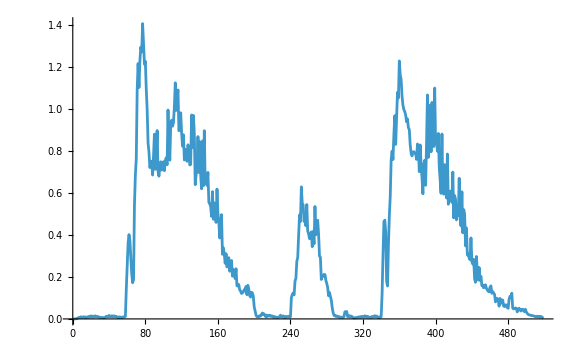

```mathematica
freqMeans=Mean/@plosiveAbs;
ListLinePlot[freqMeans,ImageSize->Large]
```

This plot is a result of graphing the average frequency of against each frame. By visualizing a curve, it now becomes clear where the peaks are, which is then extractable using FindPeaks. FindPeaks then automatically detects the first peak given a certain sharpness of the peak, which would return a point on the graph at which there is a spike in frequency; in this case, the spike occurs at window number 62, the first visibly apparent jump in frequency from near 0.

Using FindPeaks to detect a spike in frequency, adjusted with a Gaussian blurring factor of 2 and a minimum sharpness factor of 0.005 to avoid noise:

```mathematica
FindPeaks[freqMeans,2,0.005][[1]]
```

{62,0.401705}

Multiplying the duration of the audio by a proportion to obtain the time at which the plosive occurs:

```mathematica
plosiveTime=Duration[categorizedConsonants["plosives","k"],None]/Length[freqMeans]*FindPeaks[freqMeans,2,0.005][[1,1]]
```

0.240286

Approximating that the time interval at which the plosive occurs is t ± 0.1 seconds, AudioTrim the audio clip to those bounds:

```mathematica
AudioTrim[categorizedConsonants["plosives","k"],{plosiveTime-0.1,plosiveTime+0.1}]
```

The same function can be applied to voiced plosives, nasal consonants, affricates, and even click sounds alike, as the structure of all plosives and nasals are similar in that each spectrogram involves a relatively silent onset followed by a sudden burst of energy and spike in frequency. This entire process is written in the following function:

```mathematica
cropPlosive[plosive_] := Module[{freqMeans, index, t},
    freqMeans = Table[Mean[Abs /@ slice], {slice, SpectrogramArray[plosive]}];
    index = FindPeaks[freqMeans, 2, 0.005][[1, 1]];
    t = Duration[plosive, None]/Length[freqMeans]*index;
    AudioTrim[plosive, {t - 0.15, t + 0.1}]
    ]

Row[{cropPlosive[categorizedConsonants["plosives","b"]],cropPlosive[categorizedConsonants["nasals","n"]],
cropPlosive[categorizedConsonants["affricates","tʃ"]],cropPlosive[categorizedConsonants["clicks","ǁ"]]}]
```

#### 2.4.2 Devoiced Nasals

While voiceless nasals (e.g., [m̥], [n̥]) are articulated similarly to voiced nasals in terms of place and nasal airflow, the vocal folds do not vibrate unlike the latter; as a result, when voiceless nasals are articulated, it often contains a breathier and whisper-like quality. To simulate a voiceless nasal, a similar concatenative approach was taken, emulating the onset by breathing out from the nasal cavity, then attaching it to a softened voiced nasal. Ultimately, the single distinction between voiceless nasals and voiced nasals is that voiceless nasals minimize vocal fold vibration as much as possible, even if voicing and nasality align naturally and voiceless airflow through the nose is weak.

Here is the breathy onset that arises as a feature of voiceless nasals:

```mathematica
voicelessBreath=;
```

To synthesize a voiceless nasal, simply concatenate the voicelessBreath onset with faded voiced nasal counterparts:

```mathematica
synthesizeVoicelessNasal[nasal_]:=Module[{freqMeans,index,t,new},
freqMeans=Table[Mean[Abs/@slice],{slice,SpectrogramArray[nasal]}];
index=FindPeaks[freqMeans,2,0.005][[1,1]];
t=Duration[nasal,None]/Length[freqMeans]*index;
new=AudioJoin[{
AudioDelete[voicelessBreath,-0.1],
AudioOverlay[{
AudioTrim[voicelessBreath,-0.1],
AudioFade[AudioTrim[nasal,{t-0.18,t+0.15}],{0.2,0.1}]
}]
}];
new
];
```

For example, synthesizing the voiceless equivalent of the voiced velar nasal, [ŋ]:

```mathematica
synthesizeVoicelessNasal[categorizedConsonants["nasals","ŋ"]]
```

AudioOverlay is used in this function in order to smoothen out the transition between the breathy onset and the nasal consonant, as direct concatenation using AudioJoin would lead to overly choppy audio. The process of concatenating a voiced nasal into a voiceless nasal is not perfect, but it holds the essence of how voiceless nasals ideally sound.

#### 2.4.3 Fricatives

Fricatives are sibilants sounds produced through the friction of airflow at some part of the mouth. They are often characterized with a turbulent, hissing noise, in contrast to the sharp, sudden burst of a plosive or a nasal. As a result, fricatives tend to be more lengthened and stretched out in practice.

An example of a fricative consonant, [s]:

```mathematica
categorizedConsonants["fricatives","s"]
Spectrogram[%,ImageSize->800]
```

Evidently, the fricative portion of this audio can be found preceding and in between the vowel formants:

-Graphics-

One feature of fricatives like [s] is that due to its turbulent nature, it often contains a wide range of frequencies; for alveolar fricatives such as [s] and [z], including the one shown in the above example, noise energy concentrates in frequencies above 4-8 kHz (Jongman, 2024). In some way, fricatives are similar to vowels in that they can be theoretically extended indefinitely as long as the speaker can produce enough airflow, and thus the most basic model is to take a chunk of the consonant in the original data and duplicate it across windows, as done in the Vowels section. However, simply doing that results in a choppy, disconnected sound, as it fails to preserve the natural variation and turbulence of fricatives.

Duplicating a window of fricative [s] results in:

```mathematica
duplicateFricative[fricative_]:=Module[{stf,windowGroup,new},
stf=ShortTimeFourier[
AudioGenerator["Silence",0.3],
1024,512
];
windowGroup=ShortTimeFourier[fricative,1024,512][[1,1,21;;24]];

stf["Data"]=Flatten[Partition[stf["Data"],4]/.{{_Complex..}..}->windowGroup,1];

InverseShortTimeFourier[
stf,
1024,512
]
]

duplicateFricative[categorizedConsonants["fricatives","s"]]
Rasterize[Spectrogram[%,ImageSize->800]]
```

-Graphics-

Clearly, although the fricative sound is lengthened to the specified duration, simple duplication of windows simply leads to unnatural cuts and breaks in the audio. Instead, a more refined approach to fricatives would be to take a large chunk of windows from the original audio file, then use a method such as AudioTimeStretch to lengthen the duration of the audio but still preserve the natural variation and turbulence present in the original fricative.

Using AudioTimeStretch to synthesize longer fricatives:

```mathematica
synthesizeFricative[audio_,int_]:=Module[{stf,windowGroup,new},
stf=ShortTimeFourier[
AudioTrim[audio],
1024,512
];
windowGroup=stf[[1,1,int;;int+9]];
stf["Data"]=windowGroup;
new=InverseShortTimeFourier[
stf,
1024,512
];
AudioTrim[
AudioTimeStretch[new,3.5]
]
]

synthesizeFricative[categorizedConsonants["fricatives","s"],21]
Rasterize[Spectrogram[%,ImageSize->800]]
```

-Graphics-

This approach leads to a softer, smoother pronunciation, which more closely matches the natural features of the original data. Since fricatives (especially voiceless ones) often have higher frequencies which make them more difficult to perceive as a standalone, we can also concatenate a vowel at the end to accentuate its clarity.

Here is the centralized vowel, “schwa” [ə]:

```mathematica
schwa=;
```

Concatenating a schwa sound after the fricative [s]:

```mathematica
roboticConsonant[cons_]:=Module[{c1,c2,new},
c1=AudioDelete[cons,-0.1];
c2=AudioTrim[cons,-0.1];
new=AudioJoin[{
c1,AudioOverlay[{
c2,AudioFade[AudioAmplify[schwa,0.5],{0.2,0}]
}]
}];
AudioAmplify[new,1.5]
];

roboticConsonant[synthesizeFricative[categorizedConsonants["fricatives","s"],21]]
Rasterize[Spectrogram[%],ImageSize->800]
```

This spectrogram displays the synthesized pronunciation [sə] through vowel concatenation, which more clearly sets apart the fricative sound.

#### 2.4.4 Trills

Unlike flaps or taps which involve a single short, brief articulation, a trill is a consonant sound produced by rapid, repetitive vibrations by a certain part of the mouth, e.g., the tongue or lips, against another part of the vocal tract. In essence, a trill is multiple, consecutive flaps chained together to form a rolling or purring effect. To synthesize a trill consonant, we can take a flap consonant and duplicate it across multiple windows.

Take the alveolar flap [ɾ], for example:

```mathematica
categorizedConsonants["flaps","ɾ"]
Rasterize[Spectrogram[%,ImageSize->800]]
```

-Graphics-

However, one problem that arises is that there is no way to collectively identify the intervals of the flap for any given audio clip due to the rapid, single contact of the trill; if the intervals cannot be identified, then the trill cannot be produced. This is because in some cases, such as the above example, flaps are produced with a slight formant in the beginning, so it becomes difficult to use the same method to find the time intervals at which the plosive occurs as the function may detect false leaps in frequency. However, instead of finding the exact location of the flap directly, we can identify a gap in the spectrogram that signifies a break between the voiced onset and the flap, then add and subtract time to find the relative location of the flap in a given audio clip.

-Graphics--Graphics-

Using the same method of taking the averages of the magnitude of frequencies of each window as done in Section 2.4.1 on plosives, we can find dips in frequency by flipping the ListLinePlot upside down:

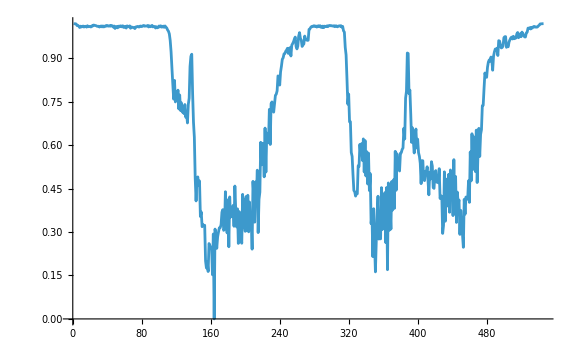

```mathematica
freqAvgs=Table[Mean[Abs/@slice],{slice,SpectrogramArray[categorizedConsonants["flaps","ɾ"]]}];
ListLinePlot[Max[freqAvgs]-freqAvgs,ImageSize->Large]
```

In the above example, the first prominent dip occurs at position number 138, where there is a clear spike vertically, indicating that there is a sudden drop in frequency at that point. Thus, we can extract the relative location of the flap given an anchor time.

```mathematica
flapIntervals[flap_]:=Module[{freqMeans,index,t,avg},
freqMeans=Table[
Mean[Abs/@slice],
{slice,SpectrogramArray[flap]
}];
index=FindPeaks[Max[freqMeans]-freqMeans,2,0.01][[1,1]];
t=Duration[flap,None]/Length[freqMeans]*index;
{t-0.015,t+0.03}
];

flapIntervals[categorizedConsonants["flaps","ɾ"]]
```

{0.519793,0.564793}

This would approximately be the time interval in which the flap occurs. Using AudioTrim to isolate the flap and RandomReal to generate gaps of random duration between each flap to simulate the natural variation in the trill, the trill can be pieced together.

```mathematica
synthesizeTrill[flap_,intervals_]:=Module[{window,new},
window=AudioTrim[
flap,intervals
];
new=AudioJoin[
Table[AudioJoin[window,AudioGenerator["Silence",RandomReal[{0.003,0.008}]]],7]
];
new
];

synthesizeTrill[
categorizedConsonants["flaps","ɾ"],
flapIntervals[categorizedConsonants["flaps","ɾ"]]
]
Rasterize[Spectrogram[%,ImageSize->800]]
```

-Graphics-

Although this is much more mechanical than a human-produced trill, e.g., , it is a good simulation as to how a trill is articulated as it mirrors the “rapid-fire” nature of an articulator vibrating on a separate part of the mouth. This function also works with other flaps as well, including the recently discovered labiodental flap, [ⱱ].

An audio synthesis of the theoretical labiodental trill:

```mathematica
synthesizeTrill[
categorizedConsonants["flaps","ⱱ"],
flapIntervals[categorizedConsonants["flaps","ⱱ"]]
]
Rasterize[Spectrogram[%,ImageSize->800]]
```

-Graphics-

## 3 Results and Conclusion

Here are the two interactive charts that play each synthesized audio for each IPA symbol:

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

This chart is incomplete.

Conclusively, non-standardized but theoretically producible vowels and consonants can be approximated through audio manipulation and modifying the frequency of the original audio data. Particularly, the sine match and cosine match of the frequency can be obtained via the short-time Fourier transform, which produces a double array of complex numbers; each complex number represents a frequency at a certain point on the spectrogram, each array of complex numbers represents a singular window of the audio, and the entire array represents the entire audio as a compilation of multiple windows. Then, the magnitude of frequency can be calculated with the real and imaginary parts of each complex data point. Modifying this magnitude allows for the change of loudness and amplitude, pitch variation, as well as the blending of multiple frequencies together; manipulating this magnitude allows for the duplication, averaging, and extraction of time intervals of certain phonetic sounds, that can help not only to identify where these sounds are in an audio clip, but also to take certain chunks of audio and map it across a stretch of audio, ultimately streamlining the synthesis process.

This project primarily took the approach of concatenative synthesis, i.e., combining audio segments of real human data into a semi-synthesized, semi-natural voice. While concatenative synthesis techniques are conventional and straightforward, other synthesis methods may produce audio that sound more natural and less choppy, or can emulate human speech without the direct reliance on pronunciation datasets. Previous research indicated that other models, such as sequence-to-sequence models like Tacotron, are more accurate in end-to-end text-to-speech synthesis, which may also be more precise in synthesizing IPA phonetics as well (Wang et. al. 2017). Thus, future improvements include both algorithmic refinements and the integration of more advanced synthesis techniques. Consonants which were too difficult to synthesize and were thus skipped included the retroflex, palatal, velar, and uvular lateral fricatives, voiceless approximants and lateral approximants, and various flaps and trills. In order to more accurately simulate these sounds, techniques may include the use of neural nets and deep learning to combine the acoustic properties of voicing, place, and manner of articulation.

## 4 Acknowledgements

This project was completed throughout the duration of the 2025 Wolfram High School Summer Research Program, hosted in Bentley College. The author is grateful to mentor Mark Greenberg for his exceptional guidance and support. His well-considered feedback were instrumental in shaping the results of this research and provided different lenses and approaches to the project. The author also extends his appreciation to mentor Logan Gilbert for his expertise in audio synthesis and manipulation, teaching assistants William Choi-Kim and Anne Shuai for providing insights on the Wolfram language and proofreading, as well as Adit Amit Kumar, Viola Pande, and Hendry Xu for peer review processes. Any remaining inadvertent errors are ours.

## 5 References

Jongman, A.  (2024, October 23). Phonetics of Fricatives. Oxford Research Encyclopedia of Linguistics. Retrieved 10 Jul. 2025, from https://oxfordre.com/linguistics/view/10.1093/acrefore/9780199384655.001.0001/acrefore-9780199384655-e-1086.

Wang, Y., Skerry-Ryan, R., Stanton, D., Wu, Y., Weiss, R. J., Jaitly, N., Yang, Z., Xiao, Y., Chen, Z., Bengio, S., Le, Q., Agiomyrgiannakis, Y., Clark, R., & Saurous, Rif A. (2017). Tacotron: Towards End-to-End Speech Synthesis. ArXiv.org. https://arxiv.org/abs/1703.10135

## 6 Appendix

### 6.1 IPA Data

```mathematica
IPAConsonantsList = {{"ɹ",},{"sʼ",},{"tʼ",},{"l",},{"ǁ",},{"ɺ",},{"n",},{"ɾ",},{"r",},{"ʘ",},{"pʼ",},{"m",},{"ʙ",},{"ǀ",},{"ʔ",},{"ɥ",},{"ʋ",},{"ⱱ",},{"ɱ",},{"j",},{"ʎ",},{"ɲ",},{"ǂ",},{"ǃ",},{"ɻ",},{"ɽ",},{"ɭ",},{"ɳ",},{"ŋ",},{"ʀ",},{"kʼ",},{"ʟ",},{"ɴ",},{"dz",},{"z",},{"ɗ",},{"ɮ",},{"d",},{"dʑ",},{"ʑ",},{"β",},{"ɓ",},{"b",},{"ð",},{"ʢ",},{"ɦ",},{"w",},{"v",},{"ʝ",},{"ʄ",},{"ɟ",},{"ʕ",},{"dʒ",},{"ʒ",},{"ɖʐ",},{"ʐ",},{"ɖ",},{"ʁ",},{"ʛ",},{"ɢ",},{"ɰ",},{"ɣ",},{"ɠ",},{"g",},{"ts",},{"s",},{"ɬ",},{"t",},{"tɕ",},{"ɕ",},{"ɸ",},{"p",},{"θ",},{"ɧ",},{"ʜ",},{"ʡ",},{"h",},{"ʍ",},{"f",},{"ç",},{"c",},{"tʃ",},{"ħ",},{"ʃ",},{"ʈʂ",},{"ʂ",},{"ʈ",},{"χ",},{"q",},{"x",},{"k",}};
IPAVowelsList={{"u",},{"ɯ",},{"ʉ",},{"ɨ",},{"y",},{"i",},{"o",},{"ɤ",},{"ɵ",},{"ɘ",},{"ø",},{"e",},{"ə",},{"ʊ",},{"ʏ",},{"ɪ",},{"ɐ",},{"æ",},{"ɒ",},{"ɑ",},{"ɶ",},{"a",},{"ɔ",},{"ʌ",},{"ɞ",},{"ɜ",},{"œ",},{"ɛ",}};
IPAConsonants = Association[IPAConsonantsList/.{IPA_,audio_}:>Rule[IPA,audio]];
IPAVowels=Association[IPAVowelsList/.{IPA_,audio_}:>Rule[IPA,audio]];

categorize[assoc_,categories__List]:=<|
Sequence@@(
With[
{label=First[#],keys=Last[#]},label->Association[#->assoc[#]&/@keys]
]&/@{categories}
)
|>

categorizedConsonants=categorize[IPAConsonants,
{"plosives",{"p","b","t","d","ʈ","ɖ","c","ɟ","k","g","q","ɢ","ʡ","ʔ"}},
{"nasals",{"m","ɱ","n","ɳ","ɲ","ŋ","ɴ"}},
{"trills",{"ʙ","r","ʀ"}},
{"flaps",{"ⱱ","ɾ","ɽ","ɺ"}},
{"fricatives",{"ɸ","β","f","v","θ","ð","s","z","ʃ","ʒ","ʂ","ʐ","ɕ","ʑ","ç","ʝ","x","ɣ","χ","ʁ","ħ","ʕ","ʜ","ʢ","h","ɦ","ɧ","ʍ"}},
{"lateralfricatives",{"ɬ","ɮ"}},
{"approximants",{"w","ʋ","ɹ","ɻ","j","ɥ","ɰ"}},
{"lateralapproximants",{"l","ɭ","ʎ","ʟ"}},
{"affricates",{"ts","tʃ","tɕ","ʈʂ","dz","dʒ","dʑ","ɖʐ"}},
{"clicks",{"ʘ","ǀ","ǃ","ǂ","ǁ"}},
{"implosives",{"ɓ","ɗ","ʄ","ɠ","ʛ"}},
{"ejectives",{"pʼ","tʼ","kʼ","sʼ"}}
];
```

### 6.2 Time-Frequency Pitch Adjust Function

```mathematica
alterFrequency[{time_,freq_}]:={
time,
freq*Piecewise[{
{0.92 ,0<time<0.15},
{0.1667(time-0.15)+0.92,0.15<time<0.45},
{0.97,time>0.45}
}]
}
```

### 6.3 Robotic Vowel Synthesizer

```mathematica
glottalOnset=AudioTrim[IPAConsonants[[Key["ʔ"]]],{1.01,1.03}];

roboticVowel[audio_,int_,n_]:=Module[{stf,window,new,aud},
stf=ShortTimeFourier[
AudioGenerator["Silence",0.5],
1024,512
];
window=ShortTimeFourier[audio,1024,512][[1,1,int]];

If[n!=1,
stf["Data"]=Flatten[
Partition[stf[[1,1]],n]/.
{a_List/;NumberQ[a[[1]]],b__List}:>{window,b},
1
],
stf=stf/.{_Complex..}:>window
];

new=InverseShortTimeFourier[
stf,1024,512
];

aud=AudioJoin[
AudioGenerator["Silence",0.05],
glottalOnset,
new
];

AudioSpectralTransformation[alterFrequency,aud]
]

synthesizedVowels=roboticVowel[#,8,1]&/@IPAVowels;
```

### 6.4 Closest Vowel to a Point, Average Vowel Function

```mathematica
closestVowels[pos_List,rounding_]:=Module[{audios,weights,anchors},
Which[
rounding=="unrounded",
anchors=<|
{-820,600}->"i",{-420,600}->"ɨ",{-20,600}->"ɯ",
{-631,500}->"ɪ",
{-687,400}->"e",{-353,400}->"ɘ",{-20,400}->"ɤ",
{-300,300}->"ə",
{-553,200}->"ɛ",{-287,200}->"ɜ",{-20,200}->"ʌ",
{-233,100}->"æ",{-466,100}->"ɐ",
{-420,0}->"a",{-20,0}->"ɑ"
|>,

rounding=="rounded",
anchors=<|
{-780,600}->"y",{-380,600}->"ʉ",{20,600}->"u",
{-591,500}->"ʏ",{-122,500}->"ʊ",
{-647,400}->"ø",{-313,400}->"ɵ",{20,400}->"o",
{-513,200}->"œ",{-247,200}->"ɞ",{20,200}->"ɔ",
{-380,0}->"ɶ",{20,0}->"ɒ"
|>

];
weights=EuclideanDistance[pos,#]&/@Nearest[Keys[anchors],pos,3];
audios=roboticVowel[IPAVowels[[Key[#]]],8,1]&/@(anchors[#]&/@Nearest[Keys[anchors],pos,3]);

If[
Total[TakeSmallest[weights,2]]<=Max[weights],
weights=TakeSmallest[weights,2];
audios=audios[[1;;2]],
Null
];

weights=(1/#)&/@weights;

{audios,weights}
]



averageVowel[{audios_List,weights_List}]:=Module[{data,w,avg,output},

avg=ShortTimeFourier[
AudioGenerator["Silence",0.5],
1024,512
];

data=ShortTimeFourier[#,1024,512]["Data"]&/@audios;

avg["Data"]=Total[
MapThread[(#1*#2)&,{data,weights}]
]/Total[weights];

output=InverseShortTimeFourier[
avg,
1024,512];

output

]
```

### 6.5 Interactive IPA Vowel Trapezoid

```mathematica
IPAVowelChart=DynamicModule[{chart,new,p={-800,40},region=Polygon[{{0,0},{-400,0},{-800,600},{0,600}}]},
chart=Graphics[{
Black,
Line[{
{-800,600},
{0,600}
}],
Line[{
{-800,600},
{-400,0}
}],
Line[{
{-400,0},
{0,0}
}],
Line[{
{0,0},
{0,600}
}],
Line[{
{-400,600},
{-200,0}
}],
Line[{
{-533,200},
{0,200}
}],
Line[{
{-667,400},
{0,400}
}],

Green,
Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["i"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["i"]]]],
Appearance->None
],{-820,600}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["y"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["y"]]]],
Appearance->None
],{-780,600}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɨ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɨ"]]]],
Appearance->None
],{-420,600}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ʉ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ʉ"]]]],
Appearance->None
],{-380,600}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɯ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɯ"]]]],
Appearance->None
],{-20,600}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["u"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["u"]]]],
Appearance->None
],{20,600}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["e"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["e"]]]],
Appearance->None
],{-687,400}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ø"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ø"]]]],
Appearance->None
],{-647,400}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɘ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɘ"]]]],
Appearance->None
],{-353,400}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɵ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɵ"]]]],
Appearance->None
],{-313,400}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɤ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɤ"]]]],
Appearance->None
],{-20,400}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["o"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["o"]]]],
Appearance->None
],{20,400}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɛ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɛ"]]]],
Appearance->None
],{-553,200}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["œ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["œ"]]]],
Appearance->None
],{-513,200}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɜ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɜ"]]]],
Appearance->None
],{-287,200}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɞ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɞ"]]]],
Appearance->None
],{-247,200}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ʌ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ʌ"]]]],
Appearance->None
],{-20,200}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɔ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɔ"]]]],
Appearance->None
],{20,200}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["a"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["a"]]]],
Appearance->None
],{-420,0}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɶ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɶ"]]]],
Appearance->None
],{-380,0}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɑ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɑ"]]]],
Appearance->None
],{-20,0}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɒ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɒ"]]]],
Appearance->None
],{20,0}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ə"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ə"]]]],
Appearance->None
],{-300,300}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɐ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɐ"]]]],
Appearance->None
],{-233,100}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["æ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["æ"]]]],
Appearance->None
],{-466,100}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ɪ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ɪ"]]]],
Appearance->None
],{-631,500}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ʏ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ʏ"]]]],
Appearance->None
],{-591,500}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["ʊ"],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[synthesizedVowels[[Key["ʊ"]]]],
Appearance->None
],{-122,500}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Orange,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["unr."],10.5,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[averageVowel[closestVowels[p,"unrounded"]]],
Appearance->None
],{-820,0}
],

Inset[
Button[
Image[
Rasterize[
Graphics[{
Orange,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text["r."],13,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[averageVowel[closestVowels[p,"rounded"]]],
Appearance->None
],{-780,0}
],

Locator[
Dynamic[p,(p=If[RegionMember[region,#],#,p])&],
Tooltip[Graphics[
{Orange,Rectangle[{-0.02,-0.02},{0.02,0.02}],Black,Style[Text["?"],14,FontFamily->"Arial"]},
ImageSize->24.5
]
]
]
},
ImageSize->Large
]; 

chart
]
```

### 6.6 Consonant Concatenation Function

```mathematica
schwa=;

roboticConsonant[cons_]:=Module[{c1,c2,new},
c1=AudioDelete[cons,-0.1];
c2=AudioTrim[cons,-0.1];
new=AudioJoin[{
c1,AudioOverlay[{
c2,AudioFade[AudioAmplify[schwa,0.5],{0.2,0}]
}]
}];
AudioAmplify[new,1.5]
];
```

### 6.7 Fricative Synthesis Function

```mathematica
synthesizeFricative[audio_,int_,duration_]:=Module[{stf,windowGroup,new},
stf=ShortTimeFourier[
AudioTrim[audio],
1024,512
];
windowGroup=stf[[1,1,int;;int+9]];
stf["Data"]=windowGroup;
new=InverseShortTimeFourier[
stf,
1024,512
];
AudioTrim[
AudioTimeStretch[new,3.5]
]
]

synthesizedFricatives=synthesizeFricative[#,20,7]&/@categorizedConsonants["fricatives"];
synthesizedFricatives["f"]=synthesizeFricative[categorizedConsonants["fricatives"]["f"],29,7];
synthesizedFricatives["v"]=synthesizeFricative[categorizedConsonants["fricatives"]["v"],29,7];
synthesizedFricatives["ʜ"]=synthesizeFricative[categorizedConsonants["fricatives"]["ʜ"],29,7];
synthesizedFricatives["ʢ"]=synthesizeFricative[categorizedConsonants["fricatives"]["ʢ"],29,7];
synthesizedFricatives["θ"]=synthesizeFricative[categorizedConsonants["fricatives"]["θ"],17,7];
synthesizedFricatives["x"]=synthesizeFricative[categorizedConsonants["fricatives"]["x"],17,7];

synthesizedFricatives=roboticConsonant[#]&/@synthesizedFricatives;
```

### 6.8 Nasal Devocalizer Function

```mathematica
voicelessBreath=;
synthesizeVoicelessNasal[nasal_]:=Module[{freqMeans,index,t,new},
freqMeans=Table[Mean[Abs/@slice],{slice,SpectrogramArray[nasal]}];
index=FindPeaks[freqMeans,2,0.005][[1,1]];
t=Duration[nasal,None]/Length[freqMeans]*index;
new=AudioJoin[{
AudioDelete[voicelessBreath,-0.1],
AudioOverlay[{
AudioTrim[voicelessBreath,-0.1],
AudioFade[AudioTrim[nasal,{t-0.15,t+0.15}],{0.2,0.1}]
}]
}];
new
]

synthesizedVoicelessNasals=synthesizeVoicelessNasal[#]&/@categorizedConsonants["nasals"];
synthesizedVoicelessNasals=AssociationThread[{"m̥","ɱ̥","n̥","ɳ̥","ɲ̥","ŋ̊","ɴ̥"},Values[synthesizedVoicelessNasals]];
```

### 6.9 Plosive Cropper Function

```mathematica
cropPlosive[plosive_]:=Module[{freqMeans,index,t},
freqMeans=Table[Mean[Abs/@slice],{slice,SpectrogramArray[plosive]}];
index=FindPeaks[freqMeans,2,0.005][[1,1]];
t=Duration[plosive,None]/Length[freqMeans]*index;
AudioTrim[plosive,{t-0.15,t+0.1}]
]

croppedPlosives=cropPlosive[#]&/@categorizedConsonants["plosives"];
croppedAffricates=cropPlosive[#]&/@categorizedConsonants["affricates"];
croppedAffricates["ts"]=cropPlosive[AudioDelete[categorizedConsonants["affricates","ts"],0.3]];
croppedNasals=cropPlosive[#]&/@categorizedConsonants["nasals"];
```

### 6.10 Flap Synthesis Function

### 6.11 Trill Synthesis Function

```mathematica
synthesizeTrill[flap_,intervals_]:=Module[{window,new},
window=AudioTrim[
flap,intervals
];
new=AudioJoin[
Table[AudioJoin[window,AudioGenerator["Silence",RandomReal[{0.003,0.008}]]],7]
];
new
];

flapIntervals[flap_]:=Module[{freqMeans,index,t,avg},
freqMeans=Table[
Mean[Abs/@slice],
{slice,SpectrogramArray[flap]
}];
index=FindPeaks[Max[freqMeans]-freqMeans,2,0.01][[1,1]];
t=Duration[flap,None]/Length[freqMeans]*index;
{t-0.015,t+0.03}
];

synthesizedTrills=synthesizeTrill[#,flapIntervals[#]]&/@categorizedConsonants["flaps"];
synthesizedTrills=AssociationThread[{"ʙ̪","r","ɽ","ɺ"},Values[synthesizedTrills]];
```

### 6.12 Interactive IPA Consonant Chart

```mathematica
ipaConsonantChart=Module[{chart,plosives,nasals,trills,flaps,fricatives},
plosives=Table[
audioButton[Keys[croppedPlosives][[i]],Values[croppedPlosives][[i]]],
{i,Range[14]}
];
plosives=Insert[plosives,unknownButton["p̪",AudioGenerator["Silence"]],3];
plosives=Insert[plosives,unknownButton["b̪",AudioGenerator["Silence"]],4];
plosives=Insert[plosives,noButton,-2];
plosives=Insert[plosives,noButton,-1];
plosives[[5]]=longButton["t",croppedPlosives["t"]];
plosives[[6]]=longButton["d",croppedPlosives["d"]];

nasals=Table[
audioButton[Riffle[Keys[synthesizedVoicelessNasals],Keys[croppedNasals]][[i]],Riffle[Values[synthesizedVoicelessNasals],Values[croppedNasals]][[i]]],
{i,Range[14]}
];
nasals[[5]]=longButton["n̥",synthesizedVoicelessNasals["n̥"]];
nasals[[6]]=longButton["n",croppedNasals["n"]];
AppendTo[nasals,#]&/@Table[noButton,4];

trills=Table[
audioButton[Keys[synthesizedTrills][[i]],Values[synthesizedTrills][[i]]],
{i,Range[3]}
];
trills=Insert[trills,unknownButton["ʙ̥",AudioGenerator["Silence"]],1];
trills=Insert[trills,audioButton["ʙ",cropPlosive[categorizedConsonants["trills","ʙ"]]],2];
trills=Insert[trills,unknownButton["ʙ̪̥",AudioGenerator["Silence"]],3];
trills[[5]]=longButton["r̥",AudioGenerator["Silence"]];
trills[[6]]=longButton["r",synthesizedTrills["r"]];
AppendTo[trills,#]&/@Table[unknownButton["",AudioGenerator["Silence"]],4];
AppendTo[trills,#]&/@Table[noButton,2];
AppendTo[trills,#]&/@Table[unknownButton["",AudioGenerator["Silence"]],4];
AppendTo[trills,#]&/@Table[noButton,2];

chart=Column[{
Row[plosives],
Row[nasals],
Row[trills]

}];

chart

]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### 6.h Helper Functions

h.1 audioButton

```mathematica
audioButton[symbol_,audio_]:=Module[{button},
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text[symbol],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[audio],
Appearance->None
]
]

unknownButton[symbol_,audio_]:=Module[{button},
Button[
Image[
Rasterize[
Graphics[{
RGBColor[0.77,1,0.77],
Rectangle[{-0.5,-0.5},{0.5,0.5}],
Black,
Style[Text[symbol],14,FontFamily->"Arial"]},
ImageSize->26
]
]
],
EmitSound[audio],
Appearance->None
]
]

noButton:=Image[
Rasterize[
Graphics[{
Lighter[Gray],
Rectangle[{-0.5,-0.5},{0.5,0.5}]},
ImageSize->26
]
]
]

longButton[symbol_,audio_]:=Module[{button},
Button[
Image[
Rasterize[
Graphics[{
Green,
Rectangle[{-1.5,-0.5},{1.5,0.5}],
Black,
Style[Text[symbol],14,FontFamily->"Arial"]},
ImageSize->78
]
]
],
EmitSound[audio],
Appearance->None
]
]
```

h.2 complexModify, complexModifyList

```mathematica
modifyComplex[num_Complex,ReIm_String,op_String,val_]:=Module[{return},
Which[
ReIm=="Re",
Which[
op=="+",return=Complex[Re[num]+val,Im[num]],
op=="-",return=Complex[Re[num]-val,Im[num]],
op=="*",return=Complex[Re[num]*val,Im[num]],
op=="/",return=Complex[Re[num]/val,Im[num]],
op=="%",return=Complex[Mod[Re[num],val],Im[num]],
op=="^",return=Complex[Re[num]^val,Im[num]],
True,return=Complex[ToExpression[op]/.ToExpression[val]:>Re[num],Im[num]]
],

ReIm=="Im",
Which[
op=="+",return=Complex[Re[num],Im[num]+val],
op=="-",return=Complex[Re[num],Im[num]-val],
op=="*",return=Complex[Re[num],Im[num]*val],
op=="/",return=Complex[Re[num],Im[num]/val],
op=="%",return=Complex[Re[num],Mod[Im[num],val]],
op=="^",return=Complex[Re[num],Im[num]^val],
True,return=Complex[Re[num],ToExpression[op]/.ToExpression[val]:>Im[num]]
]
];
return
]
```

### Notes

Goal: “Ideal” computerized, synthesized IPA sounds

Outline of project:

1. Completed consonant chart
- all existent IPA sounds
- all possible but not standardized IPA sounds
- [pa apa ap]
2. Draggable vowel trapezoid
- Use of dynamic dragger
3. Tones and pitch adjuster
4. Affricates of any two stop-fricative combination
5. Extension: word creator given IPA sounds

Functions to use:
- Spectrogram
- AudioLocalMeasurements
- Dynamic

### Test Code

```mathematica
categorizedConsonants["flaps","ⱱ"]
Spectrogram[%]

flapIntervals[categorizedConsonants["flaps","ⱱ"]]
synthesizeTrill[categorizedConsonants["flaps","ⱱ"],flapIntervals[categorizedConsonants["flaps","ⱱ"]]]
Spectrogram[%]
```

-Graphics-

{0.0547791,0.0997791}

-Graphics-

```mathematica
AudioCapture[]
```

```mathematica
Spectrogram[,PlotRange->{{0.8,1.6},Automatic}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Table[
audioButton[Keys[croppedPlosives][[i]],Values[croppedPlosives][[i]]],
{i,Range[13]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
audioButton[Riffle[Keys[synthesizedVoicelessNasals],Keys[croppedNasals]][[i]],Riffle[Values[synthesizedVoicelessNasals],Values[croppedNasals]][[i]]],
{i,Range[14]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CloudDeploy[]
```

CloudObject[https://www.wolframcloud.com/obj/6c82eb43-cbf6-4d08-b5b1-5f4151935a2f]